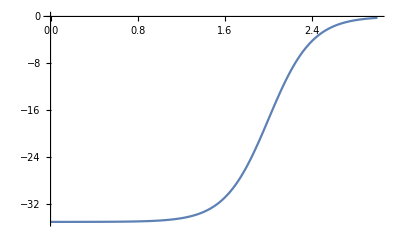

```mathematica
Subscript[m, N]=940;ℏc=197.327;
V0=35;R=2;a=0.2;μ=8/9 Subscript[m, N];
rmax=3.0;dr=0.01;
rlist=Range[0,rmax,dr];
n=Length[rlist];
V[r_]:=-V0/(1+Exp[(r-R)/a]);
Vmat=DiagonalMatrix[V[rlist]];
ListLinePlot[V[rlist],DataRange->{0,rmax}]
```

```mathematica
(*calculate Hamiltonian matrix and eigensystem*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
H0=Vmat+-ℏc^2/(2 μ) 1/dr^2(one[n,-1]-2 one[n,0]+one[n,1]);
k[En_]:=Sqrt[-(2μ En)/ℏc^2];
B[En_]:=1-dr k[En];
Hnew[En_]:=(H=H0;H[[n,n]]=Vmat[[n,n]]+-ℏc^2/(2 μ) 1/dr^2(-2+B[En]);H)
eigenv[{En_,i_}]:=({eval,evec}=Eigensystem[Hnew[En]];{eval[[-i]],i})
```

```mathematica
En=NestWhileList[eigenv,{-V0,1},Abs[#1[[1]]-#2[[1]]]>0.0000000001&,2][[-1,1]]
```

```mathematica
(*En=NestWhileList[SetPrecision[eigenv,5]{-V0,1},UnsameQ,2,100]*)
```

```mathematica
En[[-1,1]]-En[[-2,1]]
```

-1.10134×10^-12

```mathematica
eigenv[{-V0/2,1}]
```

{-7.73802,1}

```mathematica
FindRoot[eigenv[{x,1}][[1]]==x,{x,-V0/2,-V0,0},WorkingPrecision->2]
(*Plot[{eigenv[{x,1}][[1]],#&[x]},{x,-V0,0}]*)
```

$Aborted

```mathematica
wave[En_,r_]:=Exp[-k[En] r]
const[i_]:=evec[[-i,-1]]/wave[eval[[-i]],rmax]
```

```mathematica
Manipulate[ListLinePlot[{Transpose[{rlist,Abs[evec⟦-i⟧]}],Transpose[{Range[rmax,10,dr],const[i] Abs[wave[eval[[-i]],Range[rmax,10,dr]]]}]},PlotRange->All],{i,1,n,1}]
```